Задача: построить рисунок двумерного эластичного маятника, параметризованный расстоянием от центра груза до точки подвеса и углом отклонения от вертикали.

## Параметры рисунка

Груз (шарик)

```mathematica
R=1; (* радиус *)
```

Потолок

```mathematica
th=0.0075;  (* толщина линии *)
d=.35; (* период штриховки *)
```

Пружина

```mathematica
w=5; (* количество витков *)
ρ=.5; (* радиус витков *)
α=.2; (* ракурс *)
```

Область изображения

```mathematica
A=5; (* полуразмер *)
p=1.17; (* вертикальный сдвиг *)
```

## Базовое решение

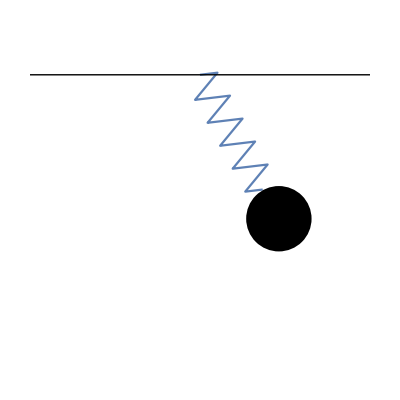

```mathematica
pic0[r_,φ_]:=
Graphics[{

InfiniteLine[{{0,0},{1,0}}], (* потолок *)

Rotate[Plot[ρ TriangleWave[w z/(r-R)],{z,0,r-R}]⟦1⟧,φ-π/2,{0,0}], (* пружина *)

Disk[{r Sin[φ],-r Cos[φ]},R] (* груз *)

},PlotRange->{{-A,A},{-2A+p,p}}];

pic0[5,.5]
```

```mathematica
Manipulate[pic0[r,φ],{{r,5},2.5,8},{{φ,.5},-π/2,π/2}]
```

## Полное решение

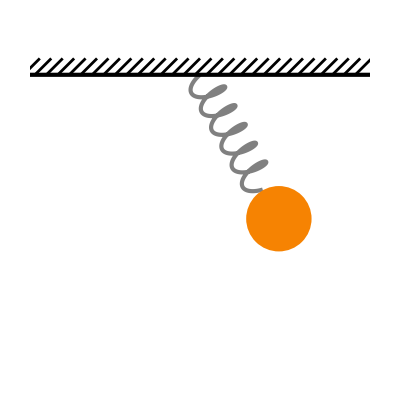

```mathematica
SpringPlot[L_]:=ParametricPlot[{ρ Cos[z+π/2],-(α (Sin[z-π/2]+1)+(L-α+α Cos[(1+2 w) π])/((1+2 w) π) z)},{z,0,(2w+1)π},
PlotStyle->Directive[Thickness[th],Gray]];
pic[r_,φ_]:=
Graphics[{

Rotate[SpringPlot[r-R]⟦1⟧,φ,{0,0}], (* пружина *)

Thickness[th],InfiniteLine[{{0,0},{1,0}}], (* потолок *)
Thickness[th/1.5],Line[{{#,0},{#+.5,.5}}]&/@Range[-1.15A,A,d], (* штриховка *)

RGBColor[{0.9647058823529412, 0.5137254901960784, 0.00784313725490196}],Disk[{r Sin[φ],-r Cos[φ]},R] (* груз *)

},PlotRange->{{-A,A},{-2A+p,p}}];

pic[5,.5]
```

```mathematica
Manipulate[pic[r,φ],{{r,5},2.5,8},{{φ,.5},-π/2,π/2}]
```

## Максимальное решение с обозначениями

```mathematica
(* груз *)
ball={
RGBColor[{0.7450980392156863, 0.4235294117647059, 0.13333333333333333}],Disk[{0,0},1], (* тень *)
RegionPlot[RegionIntersection[Disk[{0,0},1],Disk[{.2,0+.2},.95]],PlotStyle->RGBColor[{0.9647058823529412, 0.5137254901960784, 0.00784313725490196}],BoundaryStyle->None]⟦1⟧, (* силуэт *)
RGBColor[{0.9921568627450981, 0.9019607843137255, 0.8}],Rotate[Disk[{.5,.5},{.15,.1}],-π/4] (* блик *)
};
(*Graphics[ball]*)

SpringLine[L_]:=
Line@Join[{{0,0}},
ParametricPlot[{ρ Cos[z-π/2],-(.5+α (Sin[z-π/2]+1)+(L-1-α+α Cos[(1+2 w) π])/((1+2 w) π) z)},{z,0,(2w+1)π},
PlotStyle->Directive[Thickness[th],Gray]]⟦1,1,3,1,2,1⟧,
{{0,-L}}
];
(*Graphics[{RGBColor[{0.42745098039215684, 0.43137254901960786, 0.4392156862745098}],Thickness[th],SpringLine[5]}]*)

Pic[r_,φ_]:=
Graphics[{

Rotate[{RGBColor[{0.5419607843137255, 0.5450980392156863, 0.5513725490196079}],Thickness[th],SpringLine[r-R]},φ,{0,0}], (* пружина *)

Thickness[th],InfiniteLine[{{0,0},{1,0}}], (* потолок *)
Thickness[th/1.5],Line[{{#,0},{#+.5,.5}}]&/@Range[-1.15A,A,d], (* штриховка *)

Inset[Graphics[ball,PlotRangePadding->None],r{Sin[φ],-Cos[φ]},{0,0},2R] ,(* груз *)

(* обозначения *)
{RGBColor[0.07, 0.31, 0.64],
Dashing[.4/(2A)],
Line[{{0,0},{0,-5}}],
Dashing[{}],
Arrow[{{0,0},r{ Sin[φ],- Cos[φ]}}],
Inset[Style["r",24],.9r{Sin[φ],- Cos[φ]}+{0,Min[.4r Cos[φ],1]},Automatic,{1,1}],
Circle[{0,0},1.,{0,φ}-π/2],
Inset[Style["φ",24],Offset[.65 24{Sin[φ/2],-Cos[φ/2]},1.1{Sin[φ/2],-Cos[φ/2]}],Automatic,1{1,1}],
Arrow[(#+r{ Sin[φ],- Cos[φ]})&/@{{0,0},{ Sin[1],- Cos[1]}}],
Inset[Style["R",24],(r){Sin[φ],- Cos[φ]}+{0,-.6},Automatic,1{1,1}]
}
},PlotRange->{{-A,A},{-2A+p,p}}];

Pic[6,.6]
```

-Graphics-
-Graphics-

```mathematica
Manipulate[Pic[r,φ],{{r,6},2.5,8},{{φ,.6},-π/2,π/2}]
```